```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))];
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
imaginary = (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7);
real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
re1=Collect[FullSimplify[Normal[Series[real,{y,0,2}]]],y]
im1=Collect[FullSimplify[Normal[Series[imaginary,{y,0,3}]]],y]
```

μ^3 (x-x^2-(-1+x)^2 x^2 μ-(-1+x)^2 x^2 μ^2-2 (-1+x)^3 x^3 μ^3-(-1+x)^4 x^4 μ^4)+y^2 μ^3 (1+(1+6 (-1+x) x) μ+(1+6 (-1+x) x) μ^2+6 (-1+x) x (1+5 (-1+x) x) μ^3+2 (-1+x)^2 x^2 (3+14 (-1+x) x) μ^4)

-(-1+2 x) y μ^3 (1+2 (-1+x) x μ+2 (-1+x) x μ^2+6 (-1+x)^2 x^2 μ^3+4 (-1+x)^3 x^3 μ^4)-(-1+2 x) y^3 μ^3 (-2 μ-2 μ^2+2 (-1-10 (-1+x) x) μ^3+4 (-1+x) x (-1-7 (-1+x) x) μ^4)

```mathematica
x0=Solve[im1==0,x]⟦All,1⟧ (* Valores de x que levam y para 0. Note que são INdependentes de y (em ordem 1)*)
```

{x→1/2,x→1/2 (1-√(1-4 (-(-3 μ^3+14 y^2 μ^4)/(6 μ^4)+(24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)/(6 2^(2/3) μ^4 (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))-1/(12 2^(1/3) μ^4)(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3)))),x→1/2 (1+√(1-4 (-(-3 μ^3+14 y^2 μ^4)/(6 μ^4)+(24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)/(6 2^(2/3) μ^4 (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))-1/(12 2^(1/3) μ^4)(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3)))),x→1/2 (1-√(1-4 (-(-3 μ^3+14 y^2 μ^4)/(6 μ^4)-((1+ⅈ √3) (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8))/(12 2^(2/3) μ^4 (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))+1/(24 2^(1/3) μ^4)(1-ⅈ √3) (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3)))),x→1/2 (1+√(1-4 (-(-3 μ^3+14 y^2 μ^4)/(6 μ^4)-((1+ⅈ √3) (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8))/(12 2^(2/3) μ^4 (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))+1/(24 2^(1/3) μ^4)(1-ⅈ √3) (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3)))),x→1/2 (1-√(1-4 (-(-3 μ^3+14 y^2 μ^4)/(6 μ^4)-((1-ⅈ √3) (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8))/(12 2^(2/3) μ^4 (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))+1/(24 2^(1/3) μ^4)(1+ⅈ √3) (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3)))),x→1/2 (1+√(1-4 (-(-3 μ^3+14 y^2 μ^4)/(6 μ^4)-((1-ⅈ √3) (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8))/(12 2^(2/3) μ^4 (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))+1/(24 2^(1/3) μ^4)(1+ⅈ √3) (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))))}

```mathematica
x0⟦2,2⟧
```

1/2 (1-√(1-4 (-(-3 μ^3+14 y^2 μ^4)/(6 μ^4)+(24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)/(6 2^(2/3) μ^4 (-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))-1/(12 2^(1/3) μ^4)(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12+√(4 (24 μ^5-12 μ^6+96 y^2 μ^7-48 y^2 μ^8-784 y^4 μ^8)^3+(-1152 y^2 μ^9+576 y^2 μ^10-8064 y^4 μ^11+4032 y^4 μ^12+43904 y^6 μ^12)^2))^(1/3))))

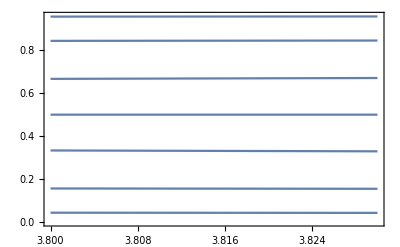

```mathematica
Plot[x0⟦All,2⟧/. y-> 0,{μ,3.8,3.83},Frame->True]
```

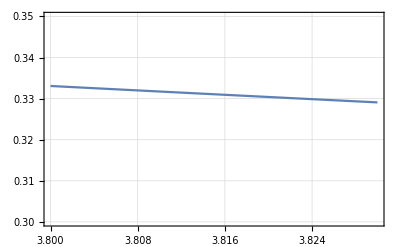

```mathematica
Plot[x0⟦All,2⟧/. y-> 0,{μ,3.8,3.83},Frame->True,PlotRange->{0,0.35},GridLines->Automatic]
```

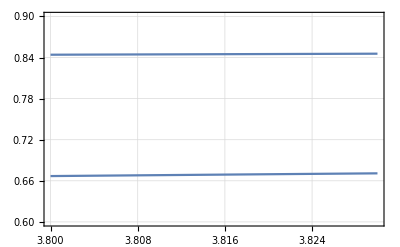

```mathematica
Plot[x0⟦All,2⟧/. y-> 0,{μ,3.8,3.83},Frame->True,PlotRange->{0.6,0.9},GridLines->Automatic]
```

```mathematica
xpos= {};
j=0;
For[mu=3.8,mu≤ 3.83,mu=mu+0.001,
j++;
For[i=1,i≤ Length[x0],i++,
xpos=AppendTo[xpos,{mu,re1/.x0⟦i⟧/.μ-> mu,y}];
]
]
(* Novos valores de x, que terão y=0 (em odem 1). Devem ser os pontos de acúmulo! Note que eles dependem do valor anterior de y (e, claro, de μ)!*)
```

```mathematica
lista=Partition[xpos,Length[x0]];
```

```mathematica
ParametricPlot3D[xpos,{y,-0.1,0.1},PlotRange->{All,{0,1},{-0.1,0.1}},BoxRatios->{1, 1, 1},ColorFunction->{#1&},ViewPoint->Top]
```

-Graphics3D-

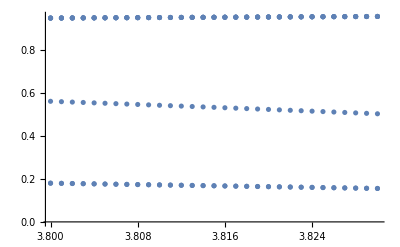

```mathematica
ListPlot[xpos⟦All,1;;2⟧/. y-> 0]
```

```mathematica
mux=xpos⟦All,1;;2⟧/. y-> 0;
```

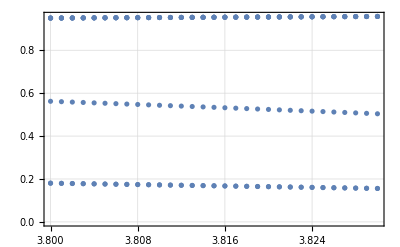

```mathematica
ListPlot[mux,GridLines->Automatic,Frame->True]
```

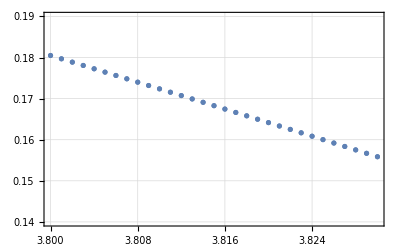

```mathematica
ListPlot[mux,GridLines->Automatic,Frame->True,PlotRange->{0.14,0.19}]
```

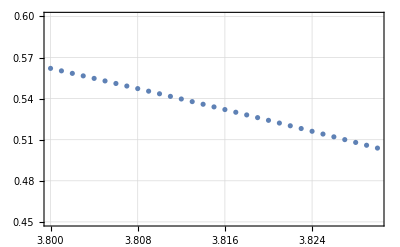

```mathematica
ListPlot[mux,GridLines->Automatic,Frame->True,PlotRange->{0.45,0.6}]
```

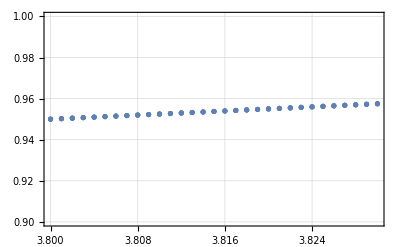

```mathematica
ListPlot[mux,GridLines->Automatic,Frame->True,PlotRange->{0.9,1}]
```

```mathematica
NSolve[{map3c[z,3.8]==z,Abs[Im[z]]< 10^0},z,Complexes]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0},{z→0.161657-0.0160987 ⅈ},{z→0.161657+0.0160987 ⅈ},{z→0.516047-0.0422187 ⅈ},{z→0.516047+0.0422187 ⅈ},{z→0.736842},{z→0.9555-0.00463191 ⅈ},{z→0.9555+0.00463191 ⅈ}}

```mathematica
map3c[z,38/10]-z/. z->0.5160468231024414-0.04221870553645675 ⅈ
```

5.10973×10^-13-1.8914×10^-13 ⅈ

```mathematica
L=Block[{μ=3.8},NSolve[{map3c[z,μ]==z,Abs[Im[z]]< 10^0},z, Complexes]]
lista={};
For[i=1,i≤  Length[L],i++,
If[L⟦i,1,2⟧== Conjugate[L⟦i,1,2⟧],AppendTo[lista,{L⟦i,1,2⟧,0,3.8}],AppendTo[lista,{Re[L⟦i,1,2⟧],Im[L⟦i,1,2⟧],3.8}]]
]
lista
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0},{z→0.161657-0.0160987 ⅈ},{z→0.161657+0.0160987 ⅈ},{z→0.516047-0.0422187 ⅈ},{z→0.516047+0.0422187 ⅈ},{z→0.736842},{z→0.9555-0.00463191 ⅈ},{z→0.9555+0.00463191 ⅈ}}

{{0,0,3.8},{0.161657,-0.0160987,3.8},{0.161657,0.0160987,3.8},{0.516047,-0.0422187,3.8},{0.516047,0.0422187,3.8},{0.736842,0,3.8},{0.9555,-0.00463191,3.8},{0.9555,0.00463191,3.8}}

```mathematica
lista={};
For[j=38/10 1000,j<384/100 1000,j++,
Block[{μ=j/1000},L=NSolve[{map3c[z,μ]==z,Abs[Im[z]]< 10^-1},z,Complexes];
For[i=1,i≤  Length[L],i++,
If[L⟦i,1,2⟧== Conjugate[L⟦i,1,2⟧],AppendTo[lista,{L⟦i,1,2⟧,0,μ}],AppendTo[lista,{Re[L⟦i,1,2⟧],Im[L⟦i,1,2⟧],μ}]]
]
]
]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

Part::partd: Part specification NSolve[{map3c[z,19/5]==z,Abs[Im[z]]<1/10},z,]⟦2,1,2⟧ is longer than depth of object.

Part::partd: Part specification NSolve[{map3c[z,19/5]==z,Abs[Im[z]]<1/10},z,]⟦3,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

General::stop: Further output of NSolve::nsmet will be suppressed during this calculation.

```mathematica
ListPointPlot3D[lista,ColorFunction->Function[{x,y,z},Hue[z]],ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[lista,ColorFunction->Function[{x,y,z},Hue[z]],PlotRange->{{0.72,0.75},{-10^-2,10^-2},Automatic}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[lista,ColorFunction->Function[{x,y,z},Hue[z]],PlotRange->{{0.95,0.96},{-10^-2,10^-2},Automatic}]
```

-Graphics3D-

```mathematica
mat = {{D[re1,x],D[re1,y]},{D[im1,x],D[im1,y]}};
mat2 ={{D[D[re1,x],x],D[D[re1,y],y]},{D[D[im1,x],x],D[D[im1,y],y]}};
```

```mathematica
autovj = Eigenvalues[mat];
autovh = Eigenvalues[mat2];
eigenvecj = Eigensystem[mat];
eigenvech = Eigensystem[mat2];
```

```mathematica
lista⟦15⟧
```

{0.955597,0.00433913,1141/300}

```mathematica
autovj/.{x-> lista⟦15,1⟧,y-> lista⟦15,2⟧,μ-> lista⟦15,3⟧}
```

{1.10607-2.57394 ⅈ,1.10607+2.57394 ⅈ}

```mathematica
autovj⟦1⟧-autovj⟦2⟧/.{x-> lista⟦15,1⟧,y-> lista⟦15,2⟧,μ-> lista⟦15,3⟧}
```

0.-5.14787 ⅈ

```mathematica
eigenvecj/.{x-> lista⟦15,1⟧,y-> lista⟦15,2⟧,μ-> lista⟦15,3⟧}
```

{{1.10607-2.57394 ⅈ,1.10607+2.57394 ⅈ},{{-0.0411729+0.999152 ⅈ,1},{-0.0411729-0.999152 ⅈ,1}}}

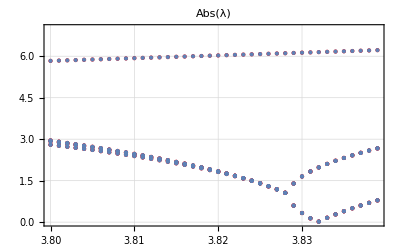

```mathematica
Show[
ListPlot[Table[{lista⟦i,3⟧,Abs[autovj⟦1⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{0,7},PlotStyle->{Red,PointSize[Medium]}],ListPlot[Table[{lista⟦i,3⟧,Abs[autovj⟦2⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{-3,3}],PlotLabel-> "Abs(λ)"]
```

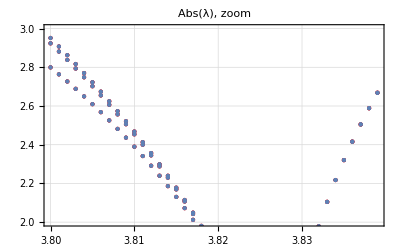

```mathematica
Show[
ListPlot[Table[{lista⟦i,3⟧,Abs[autovj⟦1⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{2,3},PlotStyle->{Red,PointSize[Medium]}],ListPlot[Table[{lista⟦i,3⟧,Abs[autovj⟦2⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{2,3}],PlotLabel-> "Abs(λ), zoom"]
```

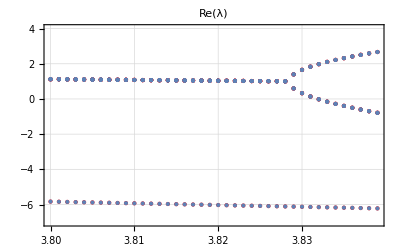

```mathematica
Show[
ListPlot[Table[{lista⟦i,3⟧,Re[autovj⟦1⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{-7,4},PlotStyle->{Red,PointSize[Medium]}],ListPlot[Table[{lista⟦i,3⟧,Re[autovj⟦2⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{-3,3}],PlotLabel-> "Re(λ)"]
```

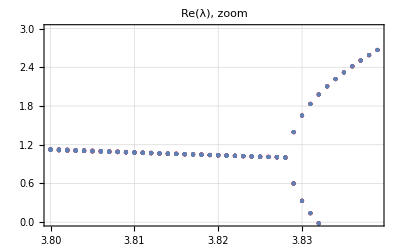

```mathematica
Show[
ListPlot[Table[{lista⟦i,3⟧,Re[autovj⟦1⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,PlotRange->{0,3},GridLines-> Automatic,PlotStyle->{Red,PointSize[Medium]}],ListPlot[Table[{lista⟦i,3⟧,Re[autovj⟦2⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{-3,3}],PlotLabel-> "Re(λ), zoom"]
```

```mathematica
Show[
ListPlot[Table[{lista⟦i,3⟧,Re[autovj⟦1⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,PlotRange->{0.99,1.15},PlotStyle->{Red,PointSize[Medium]}],ListPlot[Table[{lista⟦i,3⟧,Re[autovj⟦2⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{-3,3}],PlotLabel-> "Re(λ), zoom"]
```

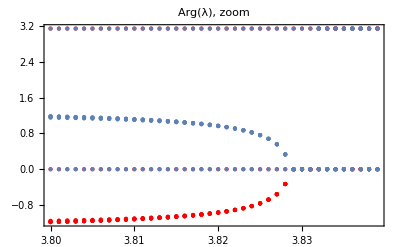

```mathematica
Show[
ListPlot[Table[{lista⟦i,3⟧,Arg[autovj⟦1⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,PlotRange->Automatic,PlotStyle->{Red,PointSize[Medium]}],ListPlot[Table[{lista⟦i,3⟧,Arg[autovj⟦2⟧]/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,GridLines->Automatic,PlotRange->{-3,3}],PlotLabel-> "Arg(λ), zoom"]
```

```mathematica
Length[autovh]
```

2

```mathematica
autovh/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}
```

{-1057043302920620001/500000000000000,0}

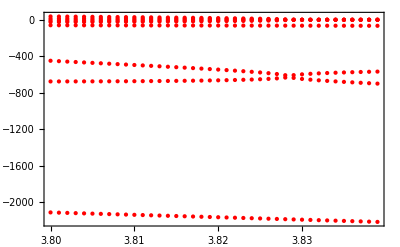

```mathematica
ListPlot[Table[{lista⟦i,3⟧,autovh⟦1⟧/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,PlotRange->Automatic,PlotStyle->{Red,PointSize[Medium]}]
```

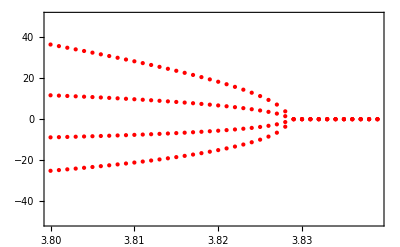

```mathematica
ListPlot[Table[{lista⟦i,3⟧,autovh⟦1⟧/.{x-> lista⟦i,1⟧,y-> lista⟦i,2⟧,μ-> lista⟦i,3⟧}},{i,1,Length[lista]}],Frame->True,PlotRange->{-50,50},PlotStyle->{Red,PointSize[Medium]}]
```

```mathematica
lista⟦3⟧
```

{0.161657,0.0160987,19/5}

11357

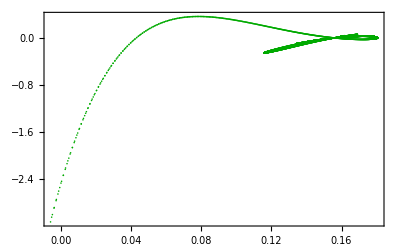

```mathematica
Block[{μ = lista⟦3,3⟧},
list1 = {};
For[j=-1,j<1,j=j+0.001,
x=lista⟦3,1⟧+lista⟦7,2⟧√(1-j^2)1/2;
y=lista⟦3,2⟧(1+j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<3,i++,
x=re1;
y = im1;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=lista⟦3,1⟧-lista⟦7,2⟧√(1-j^2)1/2;
y=lista⟦3,2⟧(1+j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<3,i++,
x=re1;
y = im1;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
]
];
Length[list1]
p1=Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{lista⟦3,1⟧,lista⟦3,2⟧}]}],PlotRange-> All]
```

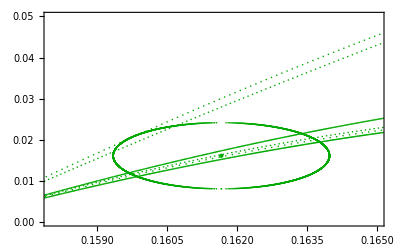

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{lista⟦3,1⟧,lista⟦3,2⟧}]}],PlotRange-> {{0.158,0.165},{0,0.05}}]
```

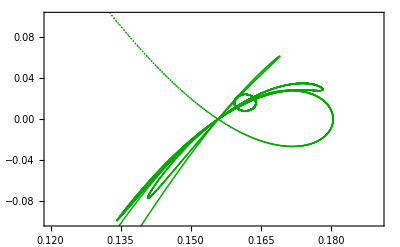

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{lista⟦3,1⟧,lista⟦3,2⟧}]}],PlotRange-> {{0.12,0.19},{-0.1,0.1}}]
```

```mathematica
lista⟦5⟧
```

{0.516047,0.0422187,19/5}

11931

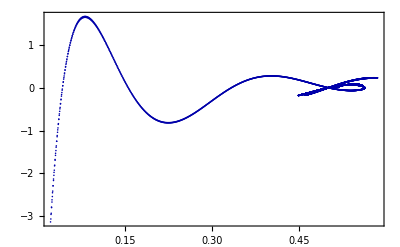

```mathematica
Block[{μ = lista⟦5,3⟧},
list1 = {};
For[j=-1,j<1,j=j+0.001,
x=lista⟦5,1⟧+lista⟦7,2⟧√(1-j^2)1/2;
y=lista⟦5,2⟧(1+j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<3,i++,
x=re1;
y = im1;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=lista⟦5,1⟧-lista⟦7,2⟧√(1-j^2)1/2;
y=lista⟦5,2⟧(1+j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<3,i++,
x=re1;
y = im1;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
]
];
Length[list1]
p2=Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{lista⟦5,1⟧,lista⟦5,2⟧}]}],PlotRange-> All]
```

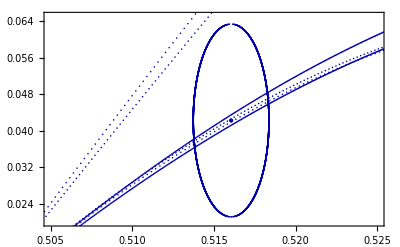

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{lista⟦5,1⟧,lista⟦5,2⟧}]}],PlotRange-> {{0.505,0.525},{0.02,0.065}}]
```

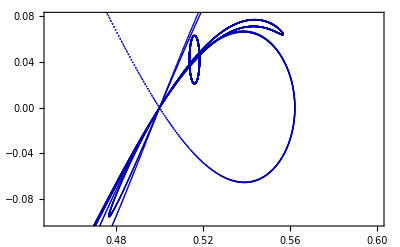

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{lista⟦5,1⟧,lista⟦5,2⟧}]}],PlotRange-> {{0.45,0.6},{-0.1,0.08}}]
```

```mathematica
lista⟦7⟧
```

{0.9555,0.00463191,19/5}

LessEqual::nord: Invalid comparison with 0.929102+4.49418×10^-10 ⅈ attempted.

LessEqual::nord: Invalid comparison with 0.929102-4.49418×10^-10 ⅈ attempted.

8002

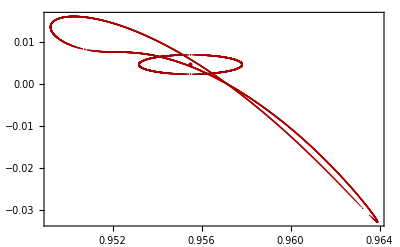

```mathematica
Block[{μ = lista⟦7,3⟧},
list1 = {};
For[j=-1,j≤ 1,j=j+0.001,
x=lista⟦7,1⟧+lista⟦7,2⟧√(1-j^2)1/2;
y=lista⟦7,2⟧(1+j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=re1;
y = im1;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
];
For[j=-1,j≤ 1,j=j+0.001,
x=lista⟦7,1⟧-lista⟦7,2⟧√(1-j^2)1/2;
y=lista⟦7,2⟧(1+j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=re1;
y = im1;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
]
];
Length[list1]
p3=Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Red]],Graphics[{Darker[Red],PointSize[Large],Point[{lista⟦7,1⟧,lista⟦7,2⟧}]}],PlotRange-> All]
```

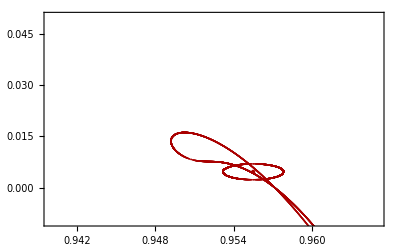

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Red]],Graphics[{Darker[Red],PointSize[Large],Point[{lista⟦7,1⟧,lista⟦7,2⟧}]}],PlotRange-> {{0.94,0.965},{-0.01,0.05}}]
```

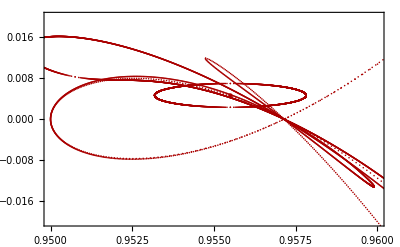

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Red]],Graphics[{Darker[Red],PointSize[Large],Point[{lista⟦7,1⟧,lista⟦7,2⟧}]}],PlotRange-> {{0.95,0.96},{-0.02,0.02}}]
```

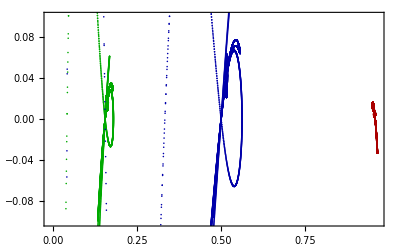

```mathematica
Show[p1,p2,p3,PlotRange-> {-0.1,0.1}]
```

```mathematica
Exp[1000.]
```

1.97007111402×10^434